```mathematica
Clear[A0i,B0i,C0i,k1i,k2i,k1bi,k2bi,time,hi,nStepsi,AData,BData,CData,AconcPrediction,BconcPrediction,CconcPrediction,An,Bn,Cn];
A0i=1.0;
B0i=0;
C0i=0;

k1i=0.01;(*A->B*)
k2i=0.2;(*B->C*)

k1bi=0.02;
k2bi=0.4;


An[0]=A0i;
Bn[0]=B0i;
Cn[0]=C0i;
```

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,k1b,k2b,A0,B0,C0];
EqnSeqB={
A'[t]==-k1 A[t] + k1b B[t],
B'[t]==k1 A[t]-k1b B[t]-k2 B[t]+k2b c[t],
c'[t]==k2 B[t]-k2b c[t],
A[0]==A0,
B[0]==B0,
c[0]==c0
};

SolSeqB=DSolve[EqnSeqB,{A[t],B[t],c[t]},t][[1]];

k1bi
k2bi

AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};
CseqB[t_]=c[t]/.Part[SolSeqB,3]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};

(*the extra 'B' in the variable names is to differentiate from previous section, where 'B' represents 'back reaction'*)
analyticalSolAB= AseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolBB =BseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolCB =CseqB[100]/.{k1b->k1bi,k2b->k2bi}
```

0.02

0.4

0.614091

0.257841

0.128068

step size: 1

0.612954, 0.258584, 0.128462,

{0.,Null}

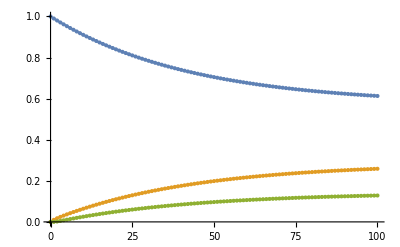

step size: 0.5

0.613523, 0.258212, 0.128265,

{0.,Null}

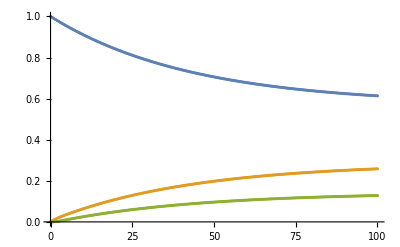

step size: 2

0.611812, 0.25933, 0.128858,

{0.,Null}

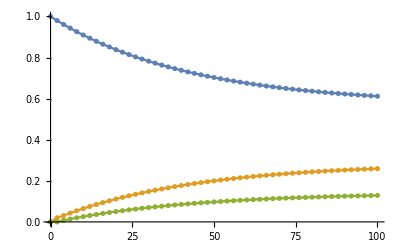

step size: 0.02

0.614068, 0.257856, 0.128076,

{0.078125,Null}

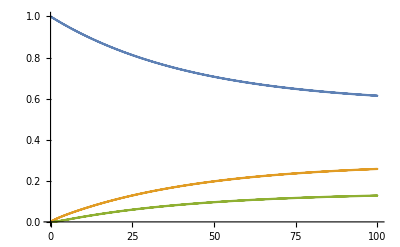

Combined plot:

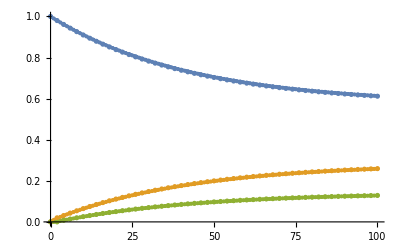

```mathematica
def[A0i_,B0i_,C0i_,hi_,k1i_,k2i_,k1bi_,k2bi_,nStepsi_]:=
Module[{A0=A0i,B0=B0i,C0=C0i,h=hi,k1=k1i,k2=k2i,k1b=k1bi,k2b=k2bi,nSteps=nStepsi},
For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h k1 An[n]+h k1b Bn[n];
Bn[n+1]=Bn[n]+h k1 An[n]-h k1b Bn[n]-h k2 Bn[n]+h k2b Cn[n];
Cn[n+1]=Cn[n]+h k2 Bn[n]-h k2b Cn[n];
];
AData=Table[{n h,An[n]},{n,0,nSteps}];
BData=Table[{n h,Bn[n]},{n,0,nSteps}];
CData=Table[{n h,Cn[n]},{n,0,nSteps}];


AconcPrediction = An[Round[100/h]];
BconcPrediction = Bn[Round[100/h]];
CconcPrediction=Cn[Round[100/h]];
Print[AconcPrediction, ", ",BconcPrediction,", ",CconcPrediction,", "];
]


time=100.0;

hi=1;
nStepsi=Round[time/hi];
Print["step size: ", hi]
Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]]
plot1= ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]]
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]]
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]]
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

```mathematica
hi=2
tVSh={};
hVSt={};
hVSerrorA={};
hVSerrorB={};
hVSerrorC={};
errorAVSh={};
errorBVSh={};
errorCVSh={};
errorABCVSh={};
errorABCtVSh={};
errorAtVSh={};
errorBtVSh={};
errorCtVSh={};

For[i=0,i<=10,i++,

hi=hi/2;
nStepsi=Round[time/hi];
Print["step size: ", hi];
Print[Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]]];

hVSt=AppendTo[hVSt,{hi,Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]]}];
tVSh=AppendTo[tVSh,{Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]],hi}];

errorA=analyticalSolAB-AconcPrediction;
errorB=analyticalSolBB-BconcPrediction;
errorC=analyticalSolCB-CconcPrediction;
hVSerrorA=AppendTo[hVSerrorA,{hi,errorA}];
hVSerrorB=AppendTo[hVSerrorB,{hi,errorB}];
hVSerrorC=AppendTo[hVSerrorC,{hi,errorC}];
errorAVSh=AppendTo[errorAVSh,{errorA,hi}];
errorBVSh=AppendTo[errorBVSh,{errorB,hi}];
errorCVSh=AppendTo[errorCVSh,{errorC,hi}];

errorABCVSh=AppendTo[errorABCVSh,{errorA,errorB,errorC,hi}];
errorABCtVSh=AppendTo[errorABCtVSh,{Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]],errorA,errorB,errorC,hi}];
errorAtVSh=AppendTo[errorAtVSh, {Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]],errorA,hi}];
errorBtVSh=AppendTo[errorBtVSh, {Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]],errorB,hi}];
errorCtVSh=AppendTo[errorCtVSh, {Timing[def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi]][[1]],errorC,hi}];

]
Print[tVSh,"\n\n",hVSt,"\n\n",hVSerrorA,"\n\n",hVSerrorB,"\n\n",hVSerrorC]
```

2

step size: 1

0.612954, 0.258584, 0.128462,

{0.03125,Null}

0.612954, 0.258584, 0.128462,

0.612954, 0.258584, 0.128462,

0.612954, 0.258584, 0.128462,

«3 more identical outputs»

step size: 1/2

0.613523, 0.258212, 0.128265,

{0.,Null}

0.613523, 0.258212, 0.128265,

0.613523, 0.258212, 0.128265,

0.613523, 0.258212, 0.128265,

«3 more identical outputs»

step size: 1/4

0.613807, 0.258027, 0.128166,

{0.,Null}

0.613807, 0.258027, 0.128166,

0.613807, 0.258027, 0.128166,

0.613807, 0.258027, 0.128166,

«3 more identical outputs»

step size: 1/8

0.613949, 0.257934, 0.128117,

{0.015625,Null}

0.613949, 0.257934, 0.128117,

0.613949, 0.257934, 0.128117,

0.613949, 0.257934, 0.128117,

«3 more identical outputs»

step size: 1/16

0.61402, 0.257887, 0.128092,

{0.03125,Null}

0.61402, 0.257887, 0.128092,

0.61402, 0.257887, 0.128092,

0.61402, 0.257887, 0.128092,

«3 more identical outputs»

step size: 1/32

0.614056, 0.257864, 0.12808,

{0.046875,Null}

0.614056, 0.257864, 0.12808,

0.614056, 0.257864, 0.12808,

0.614056, 0.257864, 0.12808,

«3 more identical outputs»

step size: 1/64

0.614073, 0.257853, 0.128074,

{0.09375,Null}

0.614073, 0.257853, 0.128074,

0.614073, 0.257853, 0.128074,

0.614073, 0.257853, 0.128074,

«3 more identical outputs»

step size: 1/128

0.614082, 0.257847, 0.128071,

{0.171875,Null}

0.614082, 0.257847, 0.128071,

0.614082, 0.257847, 0.128071,

0.614082, 0.257847, 0.128071,

«3 more identical outputs»

step size: 1/256

0.614087, 0.257844, 0.128069,

{0.34375,Null}

0.614087, 0.257844, 0.128069,

0.614087, 0.257844, 0.128069,

0.614087, 0.257844, 0.128069,

«3 more identical outputs»

step size: 1/512

0.614089, 0.257843, 0.128068,

{0.703125,Null}

0.614089, 0.257843, 0.128068,

0.614089, 0.257843, 0.128068,

0.614089, 0.257843, 0.128068,

«3 more identical outputs»

step size: 1/1024

0.61409, 0.257842, 0.128068,

{1.34375,Null}

0.61409, 0.257842, 0.128068,

0.61409, 0.257842, 0.128068,

0.61409, 0.257842, 0.128068,

«3 more identical outputs»

{{0.015625,1},{0.,1/2},{0.,1/4},{0.,1/8},{0.015625,1/16},{0.046875,1/32},{0.078125,1/64},{0.171875,1/128},{0.34375,1/256},{0.734375,1/512},{1.34375,1/1024}}

{{1,0.},{1/2,0.},{1/4,0.015625},{1/8,0.015625},{1/16,0.015625},{1/32,0.046875},{1/64,0.09375},{1/128,0.171875},{1/256,0.390625},{1/512,0.71875},{1/1024,1.39063}}

{{1,0.00113731},{1/2,0.000568079},{1/4,0.000283894},{1/8,0.00014191},{1/16,0.0000709459},{1/32,0.0000354707},{1/64,0.0000177348},{1/128,8.86724×10^-6},{1/256,4.43358×10^-6},{1/512,2.21678×10^-6},{1/1024,1.10839×10^-6}}

{{1,-0.000743053},{1/2,-0.000371149},{1/4,-0.000185479},{1/8,-0.0000927156},{1/16,-0.0000463518},{1/32,-0.0000231744},{1/64,-0.0000115868},{1/128,-5.79332×10^-6},{1/256,-2.89663×10^-6},{1/512,-1.44831×10^-6},{1/1024,-7.24154×10^-7}}

{{1,-0.000394262},{1/2,-0.000196931},{1/4,-0.0000984148},{1/8,-0.0000491947},{1/16,-0.0000245942},{1/32,-0.0000122963},{1/64,-6.14794×10^-6},{1/128,-3.07392×10^-6},{1/256,-1.53695×10^-6},{1/512,-7.68471×10^-7},{1/1024,-3.84235×10^-7}}

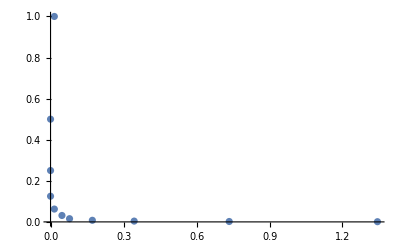

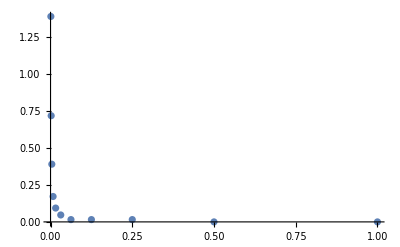

```mathematica
ListPlot[tVSh]
ListPlot[hVSt]
```